```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
Da[n_,0,a_]:=UnitStep[n-1];Da[n_,1,a_]:=Floor[n]-a
Da[n_,k_,a_]:=Sum[Binomial[k,j] Da[n/(m^(k-j)),j,m],{m,a+1,n^(1/k)},{j,0,k-1}]
Daz[n_,z_,a_]:= Sum[ bin[z,k]Da[n,k,a],{k,0,Log[a+1,n]}]
lda[n_,a_]:=Sum[(-1)^(k+1)/k Da[n,k,a],{k,1,Log[a+1,n]}]
ldf[n_,a_] := lda[n,a]-lda[n,a+1]
```

```mathematica
Expand@Daz[100,z,1]-Expand@Daz[100,z,2]
```

(7 z)/60-(572 z^2)/45+(437 z^3)/48+(605 z^4)/144+(67 z^5)/240+(7 z^6)/720

```mathematica
Expand@Daz[100,z,2]-Expand@Daz[100,z,3]
```

-(113 z)/12+(11 z^2)/24+(119 z^3)/12+z^4/24

```mathematica
Expand@Daz[100,z,3]-Expand@Daz[100,z,4]
```

-(103 z)/6+(33 z^2)/2+(5 z^3)/3

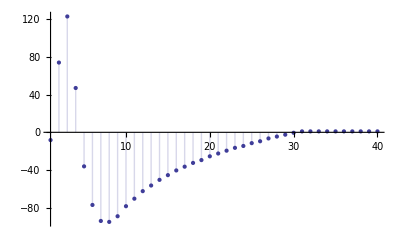

```mathematica
DiscretePlot[ ldf[1000,a],{a,1,40}]
```

```mathematica
binomial[z_,k_]:=binomial[z,k]=Product[z-j,{j,0,k-1}]/k!
Ds[n_,0,s_,a_]:=UnitStep[n-1]
Ds[n_,1,s_,a_]:=Ds[n,1,s,a]=HarmonicNumber[Floor[n],s]-HarmonicNumber[a,s]
Ds[n_,2,s_,a_]:=Ds[n,2,s,a]=Sum[(m^(-2s))+2(m^-s) (Ds[Floor[n/m],1,s,m]),{m,a+1,Floor[n^(1/2)]}]
Ds[n_,k_,s_,a_]:=Ds[n,k,s,a]=Sum[(m^(-s k))+k(m^(-s(k-1))) Ds[Floor[n/(m^(k-1))],1,s,m]+Sum[binomial[k,j] (m^-s)^j Ds[Floor[n/(m^j)],k-j,s,m],{j,1,k-2}],{m,a+1,Floor[n^(1/k)]}]

Dnka[n_,0,a_]:=UnitStep[n-1]
Dnka[n_,1,a_]:=Dnka[n,1,a]=Floor[n]-a
Dnka[n_,2,a_]:=Dnka[n,2,a]=Sum[1+2 (Dnka[Floor[n/m],1,m]),{m,a+1,Floor[n^(1/2)]}]
Dnka[n_,k_,a_]:=Dnka[n,k,a]=Sum[1+k Dnka[Floor[n/(m^(k-1))],1,m]+Sum[binomial[k,j] Dnka[Floor[n/(m^j)],k-j,m],{j,1,k-2}],{m,a+1,Floor[n^(1/k)]}]

Ddy[n_,s_,y_,k_]:=y^(k(s-1)) Ds[n y^k,k,s,y]
Ddy2[n_,s_,y_,k_]:=y^(k(s-1)) Dnka[n y^k,k,y]

Dnsyz[n_,s_,y_,z_]:=Expand@Sum[binomial[z,k]Ddy[n,s,y,k],{k,0,Log[(y+1)/y,n]}]
Dnsyz2[n_,s_,y_,z_]:=Expand@Sum[binomial[z,k]Ddy2[n,s,y,k],{k,0,Log[(y+1)/y,n]}]
```

```mathematica
Table[ N[(D[Dnsyz2[20,0,k,z],z]/.z->0) -( D[Dnsyz2[20,0,k+1,z],z]/.z->0)],{k,1,16}]
```

{1.01607,0.0334186,-0.00247749,0.0338736,0.0596889,0.0663087,0.012818,0.0261579,-0.0476362,0.0652243,-0.0179694,-0.0108422,0.0314993,-0.00573718,0.00283552,0.0336085}

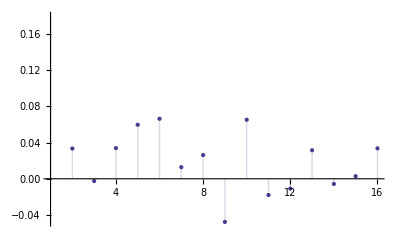

```mathematica
DiscretePlot[ N[(D[Dnsyz2[20,0,k,z],z]/.z->0) -( D[Dnsyz2[20,0,k+1,z],z]/.z->0)],{k,1,16}]
```

```mathematica
Table[(Dnsyz2[20,0,k,2]) -( Dnsyz2[20,0,k+1,2]),{k,1,20}]
```

{-6,-23/9,-145/144,-303/400,-331/450,-239/882,-1181/3136,-1283/5184,-443/4050,-1387/6050,-2099/17424,-97/1872,-205/1274,-1661/22050,-3233/57600,-7199/73984,-583/7803,61/9747,-1959/28880,-2041/35280}

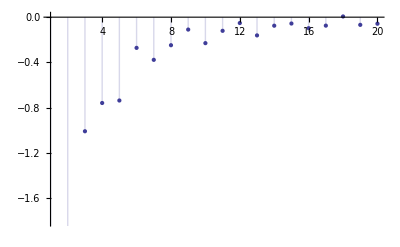

```mathematica
DiscretePlot[(Dnsyz2[20,0,k,2]) -( Dnsyz2[20,0,k+1,2]),{k,1,20}]
```

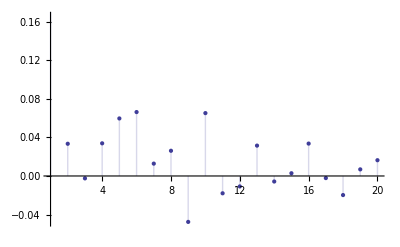

```mathematica
DiscretePlot[D[(Dnsyz2[20,0,k,z]) -( Dnsyz2[20,0,k+1,z]),z]/.z->0,{k,1,20}]
```

```mathematica
Dnsyz2[100,0,2,z]-Dnsyz2[100-1/10000000,0,2,z]
```

(3 z)/128+(107 z^2)/512+(599 z^3)/3072+(197 z^4)/3072+(25 z^5)/3072+z^6/3072

```mathematica
Dnsyz2[100,0,1,z]-Dnsyz2[99,0,1,z]
```

z^2/4+z^3/2+z^4/4

```mathematica
N@Dnsyz2[100,0,12,2]
```

552.556

```mathematica
N[Gamma[2,0,-Log[100.]]/Gamma[2]]
```

361.517-4.41506×10^-14 ⅈ

```mathematica
N@LaguerreL[-2,Log[100.]]
```

560.517